## HW 9 - #6 .6, 6.10, 6.12

### #6 .6 Mapping a Quadrilateral to a 2 x 2 Square

#### Map Element

```mathematica
Qpts ={{8,0},{5.65685, 5.65685}, {0, 8}, {0,3}, {2,0}}//TableForm
```

8 | 0
5.65685 | 5.65685
0 | 8
0 | 3
2 | 0

```mathematica
n[s_, t_] := {{-1/4(-1+s)*s*(-1+t)},{1/2(-1+s^2)*(-1+t)},{-1/4(1+s)*s*(-1+t)},{1/4(1+s)*(1+t)}, {-1/4(-1+s)*(1+t)}};
```

```mathematica
n[s,t] // MatrixForm
```

(-1/4 (-1+s) s (-1+t)
1/2 (-1+s^2) (-1+t)
-1/4 s (1+s) (-1+t)
1/4 (1+s) (1+t)
-1/4 (-1+s) (1+t))

#### Interpolated Expressions, x and y, as a function of (s, t)

```mathematica
x[s_,t_] := Qpts[[All,1]].n[s,t]
```

```mathematica
x[s,t]
```

{-2 (-1+s) s (-1+t)+2.82843 (-1+s^2) (-1+t)-1/2 (-1+s) (1+t)}

```mathematica
y[s_,t_] := Qpts[[All,2]].n[s,t]
```

```mathematica
y[s,t]
```

{-2 s (1+s) (-1+t)+2.82843 (-1+s^2) (-1+t)+3/4 (1+s) (1+t)}

#### Jacobian Matrix

```mathematica
J = ArrayReshape[Flatten[{{D[x[s,t],s],D[x[s,t],t]},{D[y[s,t],s], D[y[s,t],t]}}],{2,2}];
```

```mathematica
J //MatrixForm
```

(1/2 (-1-t)-2 (-1+s) (-1+t)+3.65685 s (-1+t) | (1-s)/2-2 (-1+s) s+2.82843 (-1+s^2)
3.65685 s (-1+t)-2 (1+s) (-1+t)+(3 (1+t))/4 | (3 (1+s))/4-2 s (1+s)+2.82843 (-1+s^2))

```mathematica
detJ = Det[J]
```

11.5992-1.41421 s+0.207106 s^2-6.02817 t+0.414212 s t-2.27817 s^2 t

#### Verify the Mapping

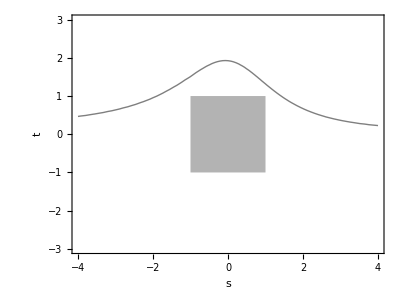

```mathematica
Block[{$DisplayFunction = Identity},
zeroContour = ContourPlot[detJ, {s,-4,4},{t,-3,3}, Contours -> {0},
ContourShading-> False, FrameLabel -> {"s","t"},
AspectRatio-> Automatic]];
Show[{zeroContour, Graphics[{GrayLevel[0.7], Rectangle[{-1,-1},{1,1}],
GrayLevel[1], Text["detJ = 0", {1.5,-2.3}]}]}]
```

### #6 .10 The Boundary Integral of a Quadrilateral Element

#### Mapping Linear Quadrilateral

```mathematica
qpts = {{2,2},{0, 3}, {0, 0}, {4,0}};
```

```mathematica
nl[s_, t_] := {{1/4(1-s)*(1-t)},{1/4(1+s)*(1-t)},{1/4(1+s)*(1+t)},{1/4(1-s)*(1+t)}}
```

```mathematica
nl[s,t] //MatrixForm
```

(1/4 (1-s) (1-t)
1/4 (1+s) (1-t)
1/4 (1+s) (1+t)
1/4 (1-s) (1+t))

```mathematica
X[s_,t_] := qpts[[All,1]].nl[s,t]
```

```mathematica
Y[s_,t_] := qpts[[All,2]].nl[s,t]
```

```mathematica
X[s,t]
```

{1/2 (1-s) (1-t)+(1-s) (1+t)}

```mathematica
Y[s,t]
```

{1/2 (1-s) (1-t)+3/4 (1+s) (1-t)}

```mathematica
j = ArrayReshape[Flatten[{{D[X[s,t],s],D[X[s,t],t]},{D[Y[s,t],s], D[Y[s,t],t]}}],{2,2}];
```

```mathematica
dj = Det[j]
```

7/4+s/2+(3 t)/4

#### Verify the Mapping

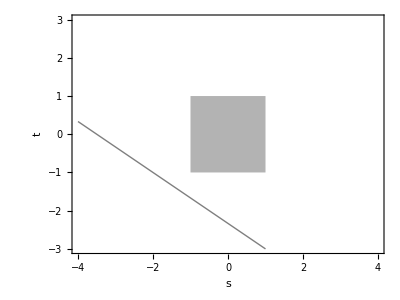

```mathematica
Block[{$DisplayFunction = Identity},
zeroContour = ContourPlot[dj, {s,-4,4},{t,-3,3}, Contours -> {0},
ContourShading-> False, FrameLabel -> {"s","t"},
AspectRatio-> Automatic]];
Show[{zeroContour, Graphics[{GrayLevel[0.7], Rectangle[{-1,-1},{1,1}],
GrayLevel[1], Text["detJ = 0", {1.5,-2.3}]}]}]
```

#### ∂N3/∂y

```mathematica
qpts[[3,2]]
```

0

```mathematica
dN3y = 1/dj*(-D[X[s,t],t]*D[ nl[s,t][[3]],s]+ D[X[s,t],s]*D[ nl[s,t][[3]],t]) /. {s -> 1,t-> 1}
```

{-1/3}

#### 1 x1 Gauss Quadrature

```mathematica
fs0 = 64*nl[s,t][[2]]*nl[s,t][[3]]
```

{4 (1+s)^2 (1-t) (1+t)}

```mathematica
ElementIntegral= 4*fs*dj  /.  {s-> 0 , t-> 0}
```

{28}

#### Boundary Integral of Side 3 using 2 point Gauss Quadrature

```mathematica
N3c = nl[s,t][[3]] /. {s -> -a, t -> 1}
```

{(1-a)/2}

```mathematica
X[-a,1]
```

{2 (1+a)}

```mathematica
Y[-a,1]
```

{0}

```mathematica
jc = D[X[-a,1],a]
```

{2}

```mathematica
i[a_] := 4*(1-a)/2*1*jc
```

```mathematica
Boundary3 = i[-0.57735]+ i[0.57735]
```

{8.}

### #6 .12 Mapping a 2D Quadrilateral Finite Element

#### Mapped Element

```mathematica
nl[s,t] // MatrixForm
```

(1/4 (1-s) (1-t)
1/4 (1+s) (1-t)
1/4 (1+s) (1+t)
1/4 (1-s) (1+t))

```mathematica
pts = {{0,0},{3, 1}, {2,3}, {-1,4}};
```

```mathematica
x1[s_,t_] := pts[[All,1]].nl[s,t]
```

```mathematica
x1[s,t]
```

{3/4 (1+s) (1-t)-1/4 (1-s) (1+t)+1/2 (1+s) (1+t)}

```mathematica
y1[s_,t_] := pts[[All,2]].nl[s,t]
```

```mathematica
y1[s,t]
```

{1/4 (1+s) (1-t)+(1-s) (1+t)+3/4 (1+s) (1+t)}

```mathematica
Ja = ArrayReshape[Flatten[{{D[x1[s,t],s],D[x1[s,t],t]},{D[y1[s,t],s], D[y1[s,t],t]}}],{2,2}]
```

{{(3 (1-t))/4+(3 (1+t))/4,1/4 (-1-s)+1/4 (-1+s)},{-1+(1-t)/4-t+(3 (1+t))/4,1+1/4 (-1-s)-s+(3 (1+s))/4}}

```mathematica
dJa = Det[Ja]
```

9/4-(3 s)/4-t/4

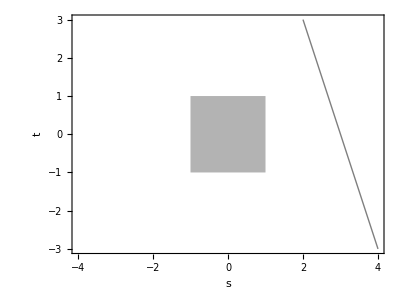

```mathematica
Block[{$DisplayFunction = Identity},
zeroContour = ContourPlot[dJa, {s,-4,4},{t,-3,3}, Contours -> {0},
ContourShading-> False, FrameLabel -> {"s","t"},
AspectRatio-> Automatic]];
Show[{zeroContour, Graphics[{GrayLevel[0.7], Rectangle[{-1,-1},{1,1}],
GrayLevel[1], Text["detJ = 0", {1.5,-2.3}]}]}]
```

#### Derivative of the Interpolation Function

```mathematica
ns = D[nl[s,t],s]
```

{{1/4 (-1+t)},{(1-t)/4},{(1+t)/4},{1/4 (-1-t)}}

```mathematica
nt = D[nl[s,t],t]
```

{{1/4 (-1+s)},{1/4 (-1-s)},{(1+s)/4},{(1-s)/4}}

```mathematica
Bx=(Ja[[2,2]]*ns - Ja[[2,1]]*nt)/dJa
```

{{(1/4 (1+1/4 (-1-s)-s+(3 (1+s))/4) (-1+t)-1/4 (-1+s) (-1+(1-t)/4-t+(3 (1+t))/4))/(9/4-(3 s)/4-t/4)},{(1/4 (1+1/4 (-1-s)-s+(3 (1+s))/4) (1-t)-1/4 (-1-s) (-1+(1-t)/4-t+(3 (1+t))/4))/(9/4-(3 s)/4-t/4)},{(1/4 (1+1/4 (-1-s)-s+(3 (1+s))/4) (1+t)-1/4 (1+s) (-1+(1-t)/4-t+(3 (1+t))/4))/(9/4-(3 s)/4-t/4)},{(1/4 (1+1/4 (-1-s)-s+(3 (1+s))/4) (-1-t)-1/4 (1-s) (-1+(1-t)/4-t+(3 (1+t))/4))/(9/4-(3 s)/4-t/4)}}

```mathematica
By =(Ja[[1,2]]*ns - Ja[[1,1]]*nt)/dJa
```

{{(1/4 (1/4 (-1-s)+1/4 (-1+s)) (-1+t)-1/4 (-1+s) ((3 (1-t))/4+(3 (1+t))/4))/(9/4-(3 s)/4-t/4)},{(1/4 (1/4 (-1-s)+1/4 (-1+s)) (1-t)-1/4 (-1-s) ((3 (1-t))/4+(3 (1+t))/4))/(9/4-(3 s)/4-t/4)},{(1/4 (1/4 (-1-s)+1/4 (-1+s)) (1+t)-1/4 (1+s) ((3 (1-t))/4+(3 (1+t))/4))/(9/4-(3 s)/4-t/4)},{(1/4 (1/4 (-1-s)+1/4 (-1+s)) (-1-t)-1/4 (1-s) ((3 (1-t))/4+(3 (1+t))/4))/(9/4-(3 s)/4-t/4)}}

```mathematica
B =ArrayReshape[Flatten[{Bx,By}],{4,2}]
```

{{(1/4 (1+1/4 (-1-s)-s+(3 (1+s))/4) (-1+t)-1/4 (-1+s) (-1+(1-t)/4-t+(3 (1+t))/4))/(9/4-(3 s)/4-t/4),(1/4 (1+1/4 (-1-s)-s+(3 (1+s))/4) (1-t)-1/4 (-1-s) (-1+(1-t)/4-t+(3 (1+t))/4))/(9/4-(3 s)/4-t/4)},{(1/4 (1+1/4 (-1-s)-s+(3 (1+s))/4) (1+t)-1/4 (1+s) (-1+(1-t)/4-t+(3 (1+t))/4))/(9/4-(3 s)/4-t/4),(1/4 (1+1/4 (-1-s)-s+(3 (1+s))/4) (-1-t)-1/4 (1-s) (-1+(1-t)/4-t+(3 (1+t))/4))/(9/4-(3 s)/4-t/4)},{(1/4 (1/4 (-1-s)+1/4 (-1+s)) (-1+t)-1/4 (-1+s) ((3 (1-t))/4+(3 (1+t))/4))/(9/4-(3 s)/4-t/4),(1/4 (1/4 (-1-s)+1/4 (-1+s)) (1-t)-1/4 (-1-s) ((3 (1-t))/4+(3 (1+t))/4))/(9/4-(3 s)/4-t/4)},{(1/4 (1/4 (-1-s)+1/4 (-1+s)) (1+t)-1/4 (1+s) ((3 (1-t))/4+(3 (1+t))/4))/(9/4-(3 s)/4-t/4),(1/4 (1/4 (-1-s)+1/4 (-1+s)) (-1-t)-1/4 (1-s) ((3 (1-t))/4+(3 (1+t))/4))/(9/4-(3 s)/4-t/4)}}

#### Gauss Points 2 x 2 Quadrature

```mathematica
p = 0.57735;
```

```mathematica
n = -0.57735;
```

```mathematica
c = {{0.5,0},{0,1.3}};
```

```mathematica
Gw = {{n,n},{n,p},{p,n},{p,p}}
```

{{-0.57735,-0.57735},{-0.57735,0.57735},{0.57735,-0.57735},{0.57735,0.57735}}

#### Numerical Integration

```mathematica
k = Table[(B/.{s -> Gw[[i,1]] , t-> Gw[[i,2]]}).c.(Bᵀ/.{s -> Gw[[i,1]] , t-> Gw[[i,2]]})*(dJa/.{s -> Gw[[i,1]] , t-> Gw[[i,2]]}),{i,1,4}];
```

```mathematica
k //MatrixForm
```

((0.310837
-0.119038
-0.095584
-0.160148) | (-0.119038
0.0466086
0.0274906
0.069082) | (-0.095584
0.0274906
0.110686
-0.019895) | (-0.160148
0.069082
-0.019895
0.141316)
(0.0309255
-0.0918957
-0.0298549
-0.0107919) | (-0.0918957
0.285809
0.0613768
0.0678988) | (-0.0298549
0.0613768
0.0874863
-0.0664717) | (-0.0107919
0.0678988
-0.0664717
0.104543)
(0.282882
-0.0637529
0.11406
0.0320262) | (-0.0637529
0.0167012
-0.0401426
0.00877478) | (0.11406
-0.0401426
0.135317
-0.0860388) | (0.0320262
0.00877478
-0.0860388
0.113239)
(0.00766488
-0.0329443
-0.00408546
0.0377914) | (-0.0329443
0.259999
-0.149847
-0.152892) | (-0.00408546
-0.149847
0.238873
-0.0336294) | (0.0377914
-0.152892
-0.0336294
0.187097))

```mathematica
kTotal= List@*Total/@k;
Kk = ArrayReshape[Flatten[kTotal], {4,4}]
```

{{-0.063933,0.0241432,0.0226978,0.0303554},{-0.101617,0.323189,0.0525366,0.0951781},{0.365215,-0.0784195,0.123195,0.0680016},{0.00842648,-0.075685,0.0513109,0.038367}}

```mathematica
Kk //MatrixForm
```

(-0.063933 | 0.0241432 | 0.0226978 | 0.0303554
-0.101617 | 0.323189 | 0.0525366 | 0.0951781
0.365215 | -0.0784195 | 0.123195 | 0.0680016
0.00842648 | -0.075685 | 0.0513109 | 0.038367)